# Experiments with only first moment

## The continuous setting

We first study a distribution with density proportional to the following, which has up the first moment, but no higher:

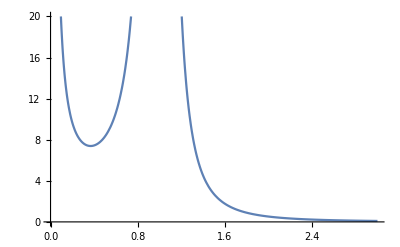

```mathematica
f[x_] := 1/(x^2 (Log[x])^2);
Plot[f[x],{x,-1,3}, PlotRange->{0,20}]
```

We’ll only keep this density from 1.5 onward, so it’s a little nicer. Next, compute the normalization factor for our density:

```mathematica
norm = Integrate[f[Abs[x]+1.5],{x,-Infinity,Infinity}]
```

1.90179

For a sanity check, make sure our denity (f divided by it’s integral) integrates to 1 and has mean 0, but also doesn’t have higher moments:

```mathematica
Integrate[f[Abs[x]+1.5]/norm, {x,-Infinity,Infinity}]
```

1.

```mathematica
Integrate[x*f[Abs[x]+1.5]/norm, {x,-Infinity,Infinity}]
```

0.

See if the 1.1 moment exists (it shouldn’t):

```mathematica
Integrate[x^(1.1)*f[Abs[x]+1.5]/norm, {x,-Infinity,Infinity}]
```

Integrate::idiv: Integral of x^1.1/(1.5  + Abs[x])^2\ Log[1.5  + Abs[x]]^2 does not converge on {-∞, ∞}.

∫_(-∞)^∞ (0.525821 x^1.1)/((1.5+Abs[x])^2 Log[1.5+Abs[x]]^2)ⅆx

Create a product distribution on R^2 using this density, reflecting across each axis and adding 1.5 to keep from dividing by 0:

```mathematica
P1 = ProbabilityDistribution[f[Abs[x]+1.5]/norm, {x, -Infinity, Infinity}];
P2 = ProbabilityDistribution[f[Abs[x]+1.5]/norm, {x, -Infinity, Infinity}];
P = ProductDistribution[P1, P2]
```

ProductDistribution[ProbabilityDistribution[0.525821/((1.5+Abs[x])^2 Log[1.5+Abs[x]]^2),{x,-∞,∞}],ProbabilityDistribution[0.525821/((1.5+Abs[x])^2 Log[1.5+Abs[x]]^2),{x,-∞,∞}]]

Let's check the mean:

```mathematica
Mean[P]
```

{0.,0.}

## A look at the Centroid Body, orthogonalization via covariance

Let’s start with looking at a sample:

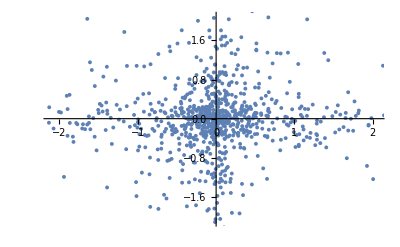

```mathematica
X = RandomVariate[P,1000];
ListPlot[X]
```

Looks a lot like Cauchy(0,1). Though the covariance matrix of the distribution is undefined, we should still get some convergence to a diagonal matrix in the empirical setting:

```mathematica
n = 100000;
X = RandomVariate[P,n];
N[MatrixForm[(1/n)*Transpose[X].X]]
```

(113.012 | 0.0369187
0.0369187 | 264.303)

Can’t seem to make the full computation of centroid body work yet...

```mathematica
toVector[t_]:={Cos[t],Sin[t]};
```

```mathematica
M[t_] := NIntegrate[Abs[({x,y}.toVector[t])]*PDF[P,{x,y}], {x,-Infinity,Infinity}, {y,-Infinity,Infinity}]
```

```mathematica
M[Pi/4]
```

NIntegrate::zeroregion: Integration region {{0.5, 1}, {1., 1.}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x, y} = {0.961031, 0.99999999999999994446110734100712972987318907258601433794648966546}. NIntegrate obtained 1.35384 and 2.47615×10^-6 for the integral and error estimates.

1.35384

So we’ll look at the empirical centroid body first:

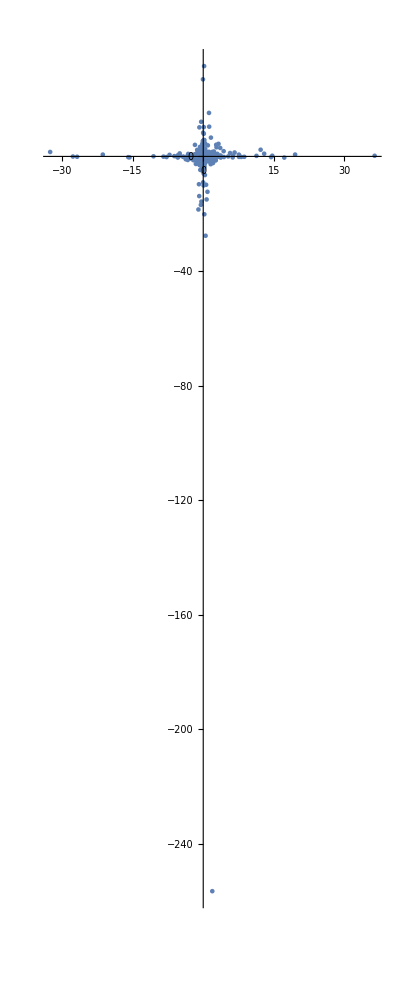

```mathematica
n = 1000;
X = RandomVariate[P,n];
Show[
PolarPlot[1/Mean[Abs[X.toVector[t]]], {t, 0, 2*Pi}, PlotStyle->{Red}],
ListPlot[X]
]
```

Finally, let’s draw a sample, and run the covariance-based orthogonalization algorithm, while still looking at the empirical centroid body:

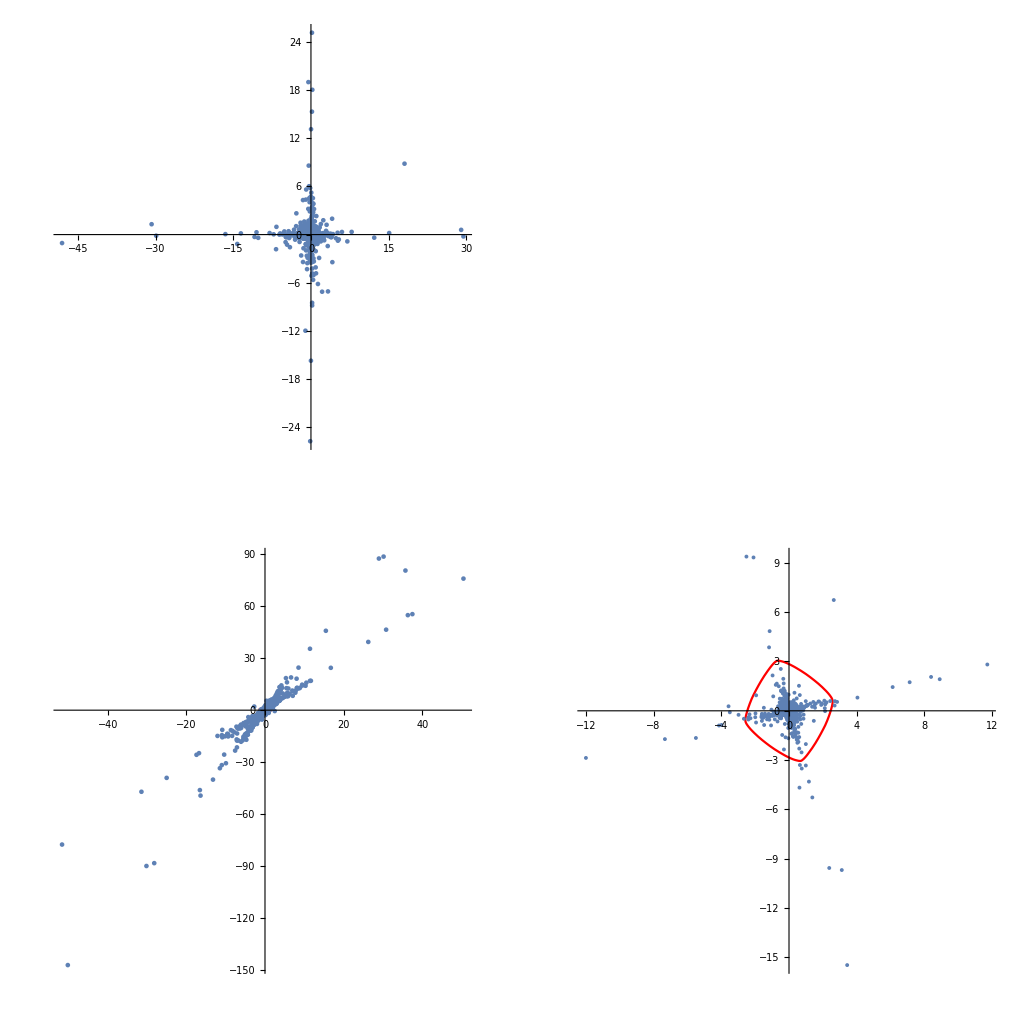

```mathematica
A = {{1,2},{3,3}};
n = 1000;
S = RandomVariate[P,n];
X = Transpose[A.Transpose[S]];
c = N[(1/n)*Transpose[X].X];
b = Inverse[MatrixPower[c,1/2]];
Y = Transpose[b.Transpose[X]];
GraphicsGrid[{
{Show[
PolarPlot[1/Mean[Abs[S.toVector[t]]], {t, 0, 2*Pi}, PlotStyle->{Red}],
ListPlot[S]
],MatrixForm[Transpose[b.A].(b.A)]},
{Show[
PolarPlot[1/Mean[Abs[X.toVector[t]]], {t, 0, 2*Pi}, PlotStyle->{Red}],
ListPlot[X]
],
Show[
PolarPlot[1/Mean[Abs[Y.toVector[t]]], {t, 0, 2*Pi}, PlotStyle->Red],
ListPlot[Y]
]}}
]
```

The empirical orthogonalization method seems promising, though on some runs it doesn’t seem to do very well... more to follow.